## Performance of ZPS for Bergmann and van Loock’s recovery procedure

M . Bergmann and P . van Loock, PRA 94, 042332 (2016)

```mathematica
𝒜:=1/(2 Cosh[T α^2]);

p0 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]+Cos[(1-γ)T α^2]) ;
p1 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]+Sin[(1-γ)T α^2]) ;
p2 := 𝒜 Cosh[γ T α^2](Cosh[(1-γ)T α^2]-Cos[(1-γ)T α^2]) ;
p3 := 𝒜 Sinh[γ T α^2](Sinh[(1-γ)T α^2]-Sin[(1-γ)T α^2]) ;

𝒩:=1/(1+2Re[a b*] Cos[T α^2]/Cosh[T α^2]);

p0Tilde[a_,b_,α_,T_,γ_] = 𝒩  p0 (1+2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p1Tilde[a_,b_,α_,T_,γ_] = 𝒩  p1 (1-2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
p2Tilde[a_,b_,α_,T_,γ_] = 𝒩  p2 (1-2 Re[a b*] Cos[γ T α^2]/Cosh[γ T α^2]);
p3Tilde[a_,b_,α_,T_,γ_] = 𝒩  p3 (1+2 Re[a b*] Sin[γ T α^2]/Sinh[γ T α^2]);
```

```mathematica
(* probability of correctable - including no error and uncorrectable errors(this is just 1-PC) *)
PC[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ]+p1Tilde[a,b,α,T,γ];
PU[a_,b_,α_,T_,γ_]=p2Tilde[a,b,α,T,γ]+p3Tilde[a,b,α,T,γ];
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

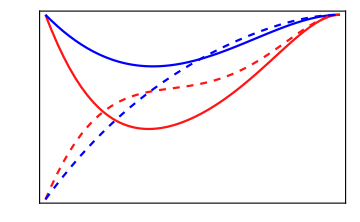

```mathematica
plt =Module[{a,ℽ,b,T1, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue},
a=1/(√2);
b =a;

α = 2;

T1=1;

ℽ[T_,η]=T/(1+(-1+T) η);

η=1;
T2=0.5;


fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];

txt[α_,x_,y_] :=Graphics[ Text[Style[MaTeX["\\alpha ="<>ToString[α],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
PC[a,b,α,T1,γ],PC[a,b,α,T2,γ],PC[a,-b,α,T1,γ],PC[a,-b,α,T2,γ]
},{γ, 0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{red,blue,{red,Dashed},{blue,Dashed}},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["P_{\\rm {c}}",Magnification->magni],None},{MaTeX["\\gamma",Magnification->magni],None}},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
g = Show[plt]
]
(*Export["zps-effectiveness-zoom out.pdf",plt]*)
```

```mathematica
<<MaTeX`
```

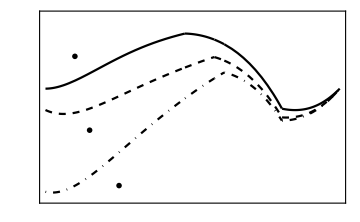

```mathematica
ClearAll[α];
PC[a_,b_,α_,T_,γ_]=p0Tilde[a,b,α,T,γ]+p1Tilde[a,b,α,T,γ];
plt =Module[{α,a,ℽ,func,b,T,T1,T2,η,γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam , magni},
a=1/(√2);
b =a;

α = 2;

T1=1;
T2=.5;

ℽ[T_,η_]:=T/(1+(-1+T) η);

func[η_]:=Min[PC[a,b,α/(√ℽ[T2,η]),T2,ℽ[T2,η](1-loss)],PC[a,-b,α/(√ℽ[T2,η]),T2,ℽ[T2,η](1-loss)]]-Min[PC[a,b,α,1,1-loss],PC[a,-b,α,1,1-loss]];

fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

txt[η_,x_,y_] :=Graphics[ Text[Style[MaTeX["\\eta ="<>ToString[η],Magnification->magni]],{x,y},{0,0}]];

red   = RGBColor["#FF1313"];
blue = RGBColor["#0000FF"];

plt=Plot[{
func[1],
func[0.75],
func[0]
}
,{loss, 0,1},PlotRange->{-0.6,0.4},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,
PlotStyle->{Black, {Black,Dashed},{Black,DotDashed}},
PlotRange->All,PlotRangeClipping->False,ImagePadding->{{80, 15}, {65, 15}},PlotRangePadding->None,
FrameLabel->{{MaTeX["\\Delta \\mathcal{F}_{\\rm {w}}",Magnification->magni],None},{MaTeX["{\\rm{loss\\ rate\\ }}(1-\\gamma)",Magnification->magni],None}},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{-0.6,-0.4,-0.2,0,0.2,0.4}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
Show[{plt,txt[1,1-0.9,0.175],txt[0.75,1-0.85,-0.225],txt[0,1-0.75,-0.525]}]
]
(*Export["nonideal-zps-perf.pdf",plt]*)
```

## Noisy ZPS vs noise after ideal ZPS

Input is an even two-component cat, of the form μ̄= 𝒩_+(ⅈ^μ α+-ⅈ^μα)

```mathematica
(* noisy ZPS *)

pLnoisyZPS[α_,T_,η_]=(Cosh[T α^2]Cosh[(1-η)(1-T)α^2])/Cosh[(1-η(1-T))α^2] ; (* probaility to stay logical *)
pEnoisyZPS[α_,T_,η_]=1-pLnoisyZPS[α,T,η] ;(* probaility of an error *)

(* ZPS then loss *)

pLZPSloss[β_,T_,γ_]= pLnoisyZPS[√T β,γ,0] ; (* probability to stay logical *)
pEZPSloss[β_,T_,γ_]=1-pLZPSloss[β,T,γ] ;(* probability of an error *)
```

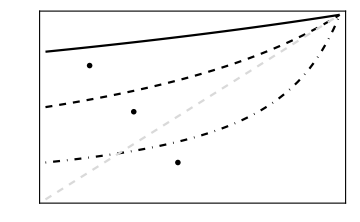

```mathematica
Module[{a,ℽ,b,T1,η, γ,plt,txt,text,xlab,ylab,xlabel, ylabel,titleSize,axesLabelSize,fam, magni ,red , blue},
ℽ[T_,η_]:=T/(1+(-1+T) η);
fam = "CMU Serif";
axesLabelSize=20;
magni =axesLabelSize/12;

txt[T_,x_,y_] :=Graphics[ Text[Style[MaTeX["T ="<>ToString[T],Magnification->magni]],{x,y},{0,0}]];

plt = Plot[{
ℽ[0.2,η],
ℽ[.5,η],
ℽ[.80,η]},{η,0,1},PlotRange->{0,1},LabelStyle->{FontSize->axesLabelSize,FontFamily->fam,Black},Frame->True,FrameStyle->BlackFrame,ImageSize->Medium,PlotStyle->{{Black,DotDashed},{Black, Dashed},Black},PlotRange->All,PlotRangeClipping->False,ImagePadding->{{65, 15}, {65, 35}},PlotRangePadding->None,
FrameLabel->{{MaTeX["\\eta'",Magnification->magni],None},{MaTeX["\\eta",Magnification->magni],Style["c",{FontSize->26.25,FontFamily->"CMU Sans Serif",Black, Bold}]}},
FrameTicks->{{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic},{Table[{x,MaTeX[x,"DisplayStyle"->False,Magnification->magni]},{x,{0,0.2,0.4,0.6,0.8,1}}],Automatic}}
];
g = Show[{plt,Plot[y,{y,0,1},PlotStyle->{Dashed, LightGray}],txt[0.2,0.45,0.2],txt[0.5,0.3,0.475],txt[0.8,0.15,0.725]}]
]
(*Export["etaprime-eta.pdf",g]*)
```